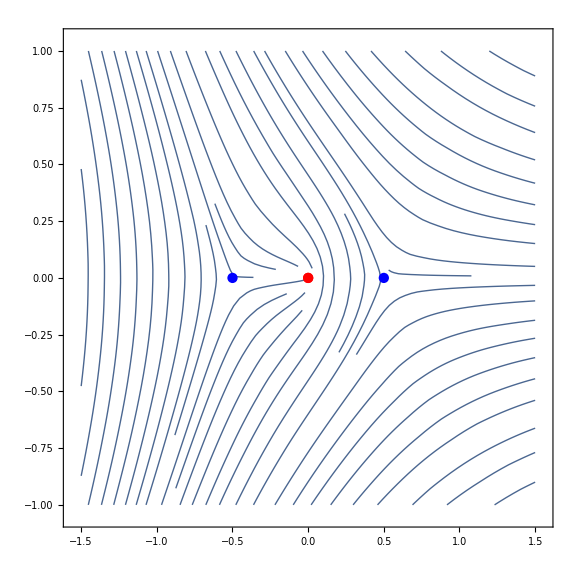
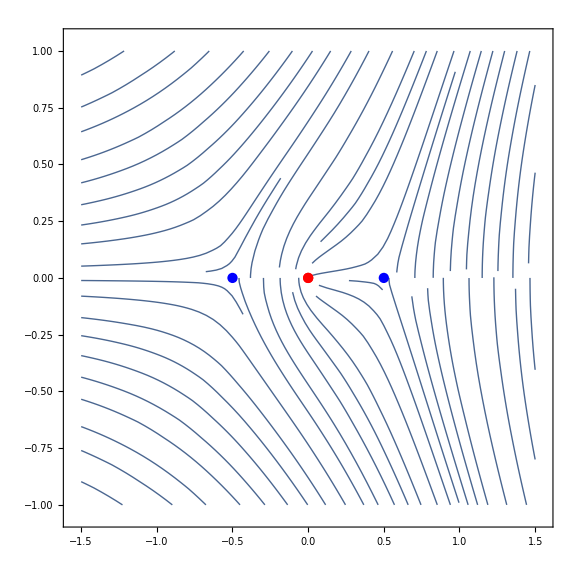

```mathematica
β=0.5;
potential=Function[x,-x+β^2/x];
StokesGraph[potential,1]
Clear[β,potential];
```

```mathematica
F=({{ⅇ^i, 0}, {r ⅇ^i, ⅇ^-i}});(*r->b+aⅇ^(-2i),F=S[b].W[i].S[a]*)
P=S[ⅈ p]ᵀ;
F.{1,0};
%⟦2⟧/%⟦1⟧//Simplify
F*.P.{1,0};
%⟦1⟧/%⟦2⟧//Simplify
```

r

1/Conjugate[r]

```mathematica
Inverse[J.F*.J]*.F*.P.{1,0};
(J.P*.J).Inverse[J.F*.J].F.{1,0}/.p*->p;
({{1, 1, Log[ρ]}, {-ⅈ(%%⟦1⟧ⅇ^(4/3 ρ^(3/2))+%%⟦2⟧), 1, (Log[ρ]+2π ⅈ)}, {ⅈ(%⟦1⟧ⅇ^(4/3 ρ^(3/2))+%⟦2⟧), 1, (Log[ρ]-2π ⅈ)}})//Det//Simplify//Apart;
D[%,ρ]/(2 √ρ)ⅇ^(-4/3 ρ^(3/2))//Simplify
%%-%ⅇ^(4/3 ρ^(3/2))//Simplify

Inverse[J.F*.J]*.F*.P.{0,1};
(J.P*.J).Inverse[J.F*.J].F.{0,1}/.p*->p;
({{1, 1, Log[ρ]}, {-ⅈ(%%⟦1⟧+%%⟦2⟧ⅇ^(-4/3 ρ^(3/2))), 1, (Log[ρ]+2π ⅈ)}, {ⅈ(%⟦1⟧+%⟦2⟧ⅇ^(-4/3 ρ^(3/2))), 1, (Log[ρ]-2π ⅈ)}})//Det//Simplify//Apart;
-D[%,ρ]/(2 √ρ)ⅇ^(4/3 ρ^(3/2))//Simplify
%%-%ⅇ^(-4/3 ρ^(3/2))//Simplify
```

0

2 π (-2 ⅈ+ⅈ ⅇ^(i+Conjugate[i]) p-ⅇ^(i-Conjugate[i]) r+ⅇ^(-i+Conjugate[i]) (1-ⅈ ⅇ^(2 i) p r) Conjugate[r])

0

2 π (-2 ⅈ+ⅈ ⅇ^(i+Conjugate[i]) p-ⅇ^(i-Conjugate[i]) r+ⅇ^(-i+Conjugate[i]) (1-ⅈ ⅇ^(2 i) p r) Conjugate[r])

```mathematica
-2 ⅈ+ⅈ ⅇ^(2Re[i]) p-ⅇ^(2Im[i]) r+ⅇ^(-2Im[i])r* -ⅈ ⅇ^(2 Re[i]) p Abs[r]^2==0;
2Re[r](ⅇ^(-2Im[i])-ⅇ^(2Im[i]))==0;
Solve[2-ⅇ^(2 Re[i]) p+2 ρ Cosh[2 Im[i]]+ⅇ^(2 Re[i]) p ρ^2==0,ρ]
```

{{ρ→(ⅇ^(-2 Re[i]) (-2 Cosh[2 Im[i]]-√2 √(1-4 ⅇ^(2 Re[i]) p+2 ⅇ^(4 Re[i]) p^2+Cosh[4 Im[i]])))/(2 p)},{ρ→(ⅇ^(-2 Re[i]) (-2 Cosh[2 Im[i]]+√2 √(1-4 ⅇ^(2 Re[i]) p+2 ⅇ^(4 Re[i]) p^2+Cosh[4 Im[i]])))/(2 p)}}

```mathematica
Integrate[ⅈ √((1-x^2)/x)ⅈ x/.x->ⅇ^(ⅈ ϕ),{ϕ,0,-π}]
```

((1-ⅈ) √π Gamma[5/4])/Gamma[7/4]

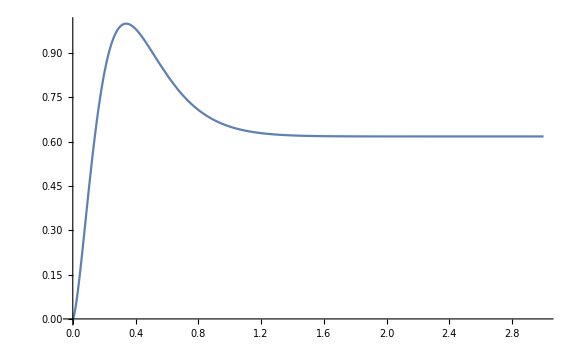

```mathematica
Plot[1-ρ^2/.ρ->(ⅇ^(-2 Re[i]) (-2 Cosh[2 Im[i]]+√2 √(1-4 ⅇ^(2 Re[i]) p+2 ⅇ^(4 Re[i]) p^2+Cosh[4 Im[i]])))/(2 p)/.i->((1-ⅈ) √π Gamma[5/4])/Gamma[7/4] β^(3/2)/.p->1(*2/3 ⅇ^(β^(3/2))(1-ⅇ^(β^(3/2)))*),{β,0,3},PlotRange->Full,ImageSize->Large]
```

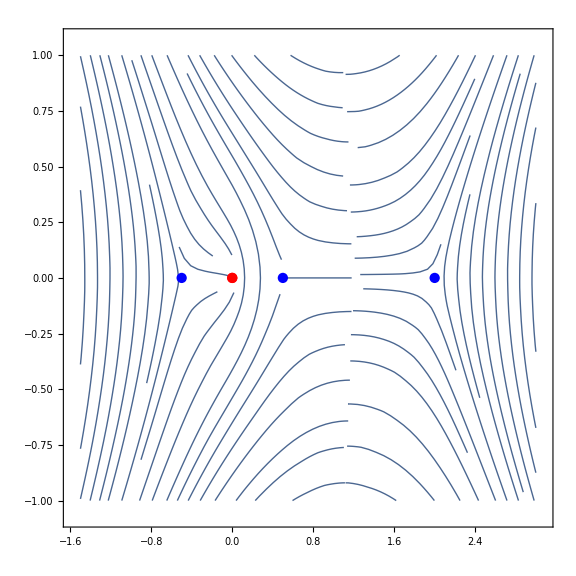
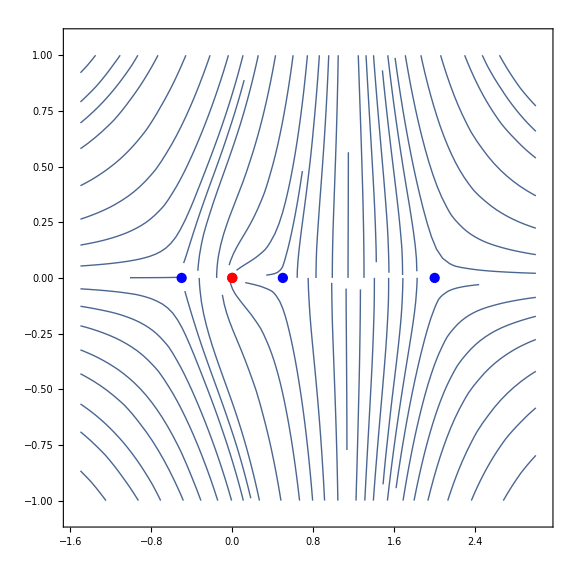

```mathematica
β=0.5;l=2;
potential=Function[x,(β^2-x^2)/x(1-x/l)];
StokesGraph[potential,1]
Clear[β,l,potential];
```

```mathematica
F=({{ⅇ^(-i-L) (1-ⅈ ⅇ^(2 L) ⅇ^(2 i)r), ⅇ^(-i+L) ⅇ^(2 i)r}, {-ⅈ ⅇ^(i+L), ⅇ^(i+L)}});(*r->b+aⅇ^(-2i),F=S[b]ᵀ.W[-i].S[a]ᵀ.W[-L].S[-ⅈ]*)
F.{1,0};
1-Abs[%⟦1⟧/%⟦2⟧]^2-Abs[1/%⟦2⟧]^2//Simplify
J.F*.J.{1,0};
1-Abs[%⟦1⟧/%⟦2⟧]^2-Abs[1/%⟦2⟧]^2//Simplify
```

1-ⅇ^(-2 Re[i+L])-ⅇ^(-4 Re[i+L]) Abs[1-ⅈ ⅇ^(2 (i+L)) r]^2

-(1+ⅇ^(-2 Re[i+L])-Abs[r]^2)/Abs[r]^2

```mathematica
Inverse[F].(J.F*.J).{1,0};
Inverse[J.F*.J].F.{1,0};
({{1, 1, Log[ρ]}, {-(%%⟦1⟧+%%⟦2⟧ⅇ^(-ⅈ 2 ρ^2)), 1, (Log[ρ]+2π ⅈ)}, {-(%⟦1⟧+%⟦2⟧ⅇ^(-ⅈ 2 ρ^2)), 1, (Log[ρ]-2π ⅈ)}})/.(i+L)*->i*+L/.L*->L//Det//Simplify//Apart;
D[%,ρ]/(-4ⅈ ρ)ⅇ^(ⅈ 2 ρ^2)//Simplify
%%-%ⅇ^(-ⅈ 2 ρ^2)//Simplify

Inverse[F].(J.F*.J).{0,1};
Inverse[J.F*.J].F.{0,1};
({{1, 1, Log[ρ]}, {-(%%⟦1⟧ⅇ^(ⅈ 2 ρ^2)+%%⟦2⟧), 1, (Log[ρ]+2π ⅈ)}, {-(%⟦1⟧ⅇ^(ⅈ 2 ρ^2)+%⟦2⟧), 1, (Log[ρ]-2π ⅈ)}})/.(i+L)*->i*+L/.L*->L//Det//Simplify//Apart;
D[%,ρ]/(4ⅈ ρ)ⅇ^(-ⅈ 2 ρ^2)//Simplify
%%-%ⅇ^(ⅈ 2 ρ^2)//Simplify
```

0

2 π (-2 ⅈ+ⅇ^(-i-2 L-Conjugate[i]) (-ⅈ-ⅇ^(2 (i+L)) r)+ⅇ^(-i+Conjugate[i]) Conjugate[r])

0

2 π (-2 ⅈ+ⅇ^(-i-2 L-Conjugate[i]) (-ⅈ-ⅇ^(2 (i+L)) r)+ⅇ^(-i+Conjugate[i]) Conjugate[r])

```mathematica
Limit[-2 ⅈ+ⅇ^(-i-2 L-Conjugate[i]) (-ⅈ-ⅇ^(2 (i+L)) r)+ⅇ^(-i+Conjugate[i]) Conjugate[r],L->Infinity]
```

-2 ⅈ-ⅇ^(i-Conjugate[i]) r+ⅇ^(-i+Conjugate[i]) Conjugate[r]

```mathematica
Solve[-2 ⅈ-ⅇ^(2Im[i]) r+ⅇ^(-2Im[i]) Conjugate[r]==0,r]
```

{{r→-(2 ⅈ)/(ⅇ^(-2 Im[i])+ⅇ^(2 Im[i]))}}

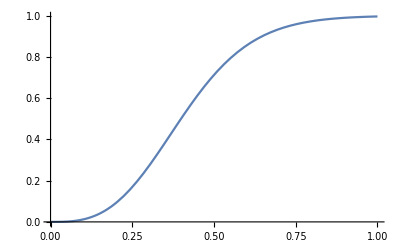

```mathematica
Plot[1-Abs[r]^2/.r->-ⅈ/Cosh[2 Im[i]]/.i->((1-ⅈ) √π Gamma[5/4])/Gamma[7/4] β^(3/2),{β,0,1}]
```